```mathematica
AppendTo[$Path,FileNameJoin[{$HomeDirectory,"GDC","DialecticalStructures"}]];
If[!MemberQ[$Path,FileNameJoin[{$HomeDirectory,"GDC","DialecticalStructures"}]],AppendTo[$Path,FileNameJoin[{$HomeDirectory,"GDC","DialecticalStructures"}]]];
Print["Package path ",FindFile["GDCAnalysis3`"]];
Print["Package path ",FindFile["GDCComparisons`"]];
<<GDCComparisons`
<<GDCAnalysis3`
```

Package path /home/carla/GDC/DialecticalStructures/GDCAnalysis3.m

Package path /home/carla/GDC/DialecticalStructures/GDCComparisons.m

tableFunc::shdw: Symbol tableFunc appears in multiple contexts {DialecticalStructures`GDCComparisons`,Global`}; definitions in context DialecticalStructures`GDCComparisons` may shadow or be shadowed by other definitions.

```mathematica
tsAR={0,1,2,3,4,5,6,7,8};
tsALLRed=Drop[tsAR,1]
tatCH=Map[Get[#]&,FileNames["/home/carla/GDC/POS/*.txt"]];
```

{1,2,3,4,5,6,7,8}

```mathematica
cDLBMUR=arrayFunc[First[persMixFunc["DLB"]],First[persMixFunc["MUR"]],0,tsALLRed, tatCH, "CH", "PEN"];
cDLBLYE=arrayFunc[First[persMixFunc["DLB"]],First[persMixFunc["LYE"]],0,tsALLRed, tatCH, "CH", "PEN"];
cDLBPHI=arrayFunc[First[persMixFunc["DLB"]],First[persMixFunc["PHI"]],1,tsALLRed, tatCH, "CH", "PEN"];
cDLBSED=arrayFunc[First[persMixFunc["DLB"]],First[persMixFunc["SED"]],2,tsALLRed, tatCH, "CH", "PEN"];
cDLBAUS=arrayFunc[First[persMixFunc["DLB"]],First[persMixFunc["AUS"]],5,tsALLRed, tatCH, "CH", "PEN"];
cMURLYE=arrayFunc[First[persMixFunc["MUR"]],First[persMixFunc["LYE"]],0,tsALLRed, tatCH, "CH", "PEN"];
cMURPHI=arrayFunc[First[persMixFunc["MUR"]],First[persMixFunc["PHI"]],1,tsALLRed, tatCH, "CH", "PEN"];
cMURSED=arrayFunc[First[persMixFunc["MUR"]],First[persMixFunc["SED"]],2,tsALLRed, tatCH, "CH", "PEN"];
cMURAUS=arrayFunc[First[persMixFunc["MUR"]],First[persMixFunc["AUS"]],5,tsALLRed, tatCH, "CH", "PEN"];
cLYEPHI=arrayFunc[First[persMixFunc["LYE"]],First[persMixFunc["PHI"]],1,tsALLRed, tatCH, "CH", "PEN"];
cLYESED=arrayFunc[First[persMixFunc["LYE"]],First[persMixFunc["SED"]],2,tsALLRed, tatCH, "CH", "PEN"];
cLYEAUS=arrayFunc[First[persMixFunc["LYE"]],First[persMixFunc["AUS"]],5,tsALLRed, tatCH, "CH", "PEN"];
cPHISED=arrayFunc[First[persMixFunc["PHI"]],First[persMixFunc["SED"]],2,tsALLRed, tatCH, "CH", "PEN"];
cPHIAUS=arrayFunc[First[persMixFunc["PHI"]],First[persMixFunc["AUS"]],5,tsALLRed, tatCH, "CH", "PEN"];
cSEDAUS=arrayFunc[First[persMixFunc["SED"]],First[persMixFunc["AUS"]],5,tsALLRed, tatCH, "CH", "PEN"];
dataToPlot=<|"DLB"->{cDLBMUR,cDLBLYE,cDLBPHI,cDLBSED,cDLBAUS}, "MUR"-> {cDLBMUR,cMURLYE,cMURPHI,cMURSED,cMURAUS},
"LYE"->  {cDLBLYE,cMURLYE,cLYEPHI,cLYESED,cLYEAUS},"PHI"->  {cDLBPHI,cMURPHI,cLYEPHI,cPHISED,cPHIAUS}, "SED"->  {cDLBSED,cMURSED,cLYESED,cPHISED,cSEDAUS},
"AUS"->  {cDLBAUS,cMURAUS,cLYEAUS, cPHIAUS,cSEDAUS}|>;
```

```mathematica
(*dataToPlot[["DLB"]][[1]]
Length[dataToPlot[["DLB"]][[1]]]*)
dMin=First[Min[Flatten[Values[dataToPlot]]]]
dMax=First[Max[Flatten[Values[dataToPlot]]]]
names={"DLB","MUR","LYE","PHI","SED","AUS"}
```

0.6

1.

{DLB,MUR,LYE,PHI,SED,AUS}

```mathematica
dataPersTables=Map[tableFunc[dataToPlot, #, "RED"]&,names];
dataPersTableOut=Column[Map[dataPersTables[[#]]&,Range[6]]]
```

DLB Compared With | S1 | S2 | S3 | S4 | S5 | S6 | S7 | S8
MUR | 0.733333 | 0.733333 | 0.666667 | 0.733333 | 0.666667 | 0.666667 | 0.6 | 1.
LYE | 0.733333 | 0.733333 | 0.666667 | 0.733333 | 0.733333 | 0.666667 | 0.6 | 1.
PHI | GrayLevel[1] | 1. | 1. | 0.733333 | 0.733333 | 0.666667 | 0.666667 | 1.
SED | GrayLevel[1] | GrayLevel[1] | 0.666667 | 0.733333 | 0.733333 | 0.666667 | 0.666667 | 1.
AUS | GrayLevel[1] | GrayLevel[1] | GrayLevel[1] | GrayLevel[1] | GrayLevel[1] | 0.733333 | 0.733333 | 1.
MUR Compared With | S1 | S2 | S3 | S4 | S5 | S6 | S7 | S8
DLB | 0.733333 | 0.733333 | 0.666667 | 0.733333 | 0.666667 | 0.666667 | 0.6 | 1.
LYE | 1. | 1. | 1. | 1. | 0.933333 | 1. | 1. | 1.
PHI | GrayLevel[1] | 0.733333 | 0.666667 | 0.866667 | 0.8 | 1. | 0.8 | 1.
SED | GrayLevel[1] | GrayLevel[1] | 1. | 0.866667 | 0.8 | 0.866667 | 0.666667 | 1.
AUS | GrayLevel[1] | GrayLevel[1] | GrayLevel[1] | GrayLevel[1] | GrayLevel[1] | 0.933333 | 0.866667 | 1.
LYE Compared With | S1 | S2 | S3 | S4 | S5 | S6 | S7 | S8
DLB | 0.733333 | 0.733333 | 0.666667 | 0.733333 | 0.733333 | 0.666667 | 0.6 | 1.
MUR | 1. | 1. | 1. | 1. | 0.933333 | 1. | 1. | 1.
PHI | GrayLevel[1] | 0.733333 | 0.666667 | 0.866667 | 0.866667 | 1. | 0.8 | 1.
SED | GrayLevel[1] | GrayLevel[1] | 1. | 0.866667 | 0.866667 | 0.866667 | 0.666667 | 1.
AUS | GrayLevel[1] | GrayLevel[1] | GrayLevel[1] | GrayLevel[1] | GrayLevel[1] | 0.933333 | 0.866667 | 1.
PHI Compared With | S1 | S2 | S3 | S4 | S5 | S6 | S7 | S8
DLB | GrayLevel[1] | 1. | 1. | 0.733333 | 0.733333 | 0.666667 | 0.666667 | 1.
MUR | GrayLevel[1] | 0.733333 | 0.666667 | 0.866667 | 0.8 | 1. | 0.8 | 1.
LYE | GrayLevel[1] | 0.733333 | 0.666667 | 0.866667 | 0.866667 | 1. | 0.8 | 1.
SED | GrayLevel[1] | GrayLevel[1] | 0.666667 | 1. | 1. | 0.866667 | 0.866667 | 1.
AUS | GrayLevel[1] | GrayLevel[1] | GrayLevel[1] | GrayLevel[1] | GrayLevel[1] | 0.933333 | 0.933333 | 1.
SED Compared With | S1 | S2 | S3 | S4 | S5 | S6 | S7 | S8
DLB | GrayLevel[1] | GrayLevel[1] | 0.666667 | 0.733333 | 0.733333 | 0.666667 | 0.666667 | 1.
MUR | GrayLevel[1] | GrayLevel[1] | 1. | 0.866667 | 0.8 | 0.866667 | 0.666667 | 1.
LYE | GrayLevel[1] | GrayLevel[1] | 1. | 0.866667 | 0.866667 | 0.866667 | 0.666667 | 1.
PHI | GrayLevel[1] | GrayLevel[1] | 0.666667 | 1. | 1. | 0.866667 | 0.866667 | 1.
AUS | GrayLevel[1] | GrayLevel[1] | GrayLevel[1] | GrayLevel[1] | GrayLevel[1] | 0.8 | 0.8 | 1.
AUS Compared With | S1 | S2 | S3 | S4 | S5 | S6 | S7 | S8
DLB | GrayLevel[1] | GrayLevel[1] | GrayLevel[1] | GrayLevel[1] | GrayLevel[1] | 0.733333 | 0.733333 | 1.
MUR | GrayLevel[1] | GrayLevel[1] | GrayLevel[1] | GrayLevel[1] | GrayLevel[1] | 0.933333 | 0.866667 | 1.
LYE | GrayLevel[1] | GrayLevel[1] | GrayLevel[1] | GrayLevel[1] | GrayLevel[1] | 0.933333 | 0.866667 | 1.
PHI | GrayLevel[1] | GrayLevel[1] | GrayLevel[1] | GrayLevel[1] | GrayLevel[1] | 0.933333 | 0.933333 | 1.
SED | GrayLevel[1] | GrayLevel[1] | GrayLevel[1] | GrayLevel[1] | GrayLevel[1] | 0.8 | 0.8 | 1.

```mathematica
dataPersArray=Map[Function[y,ArrayPlot[dataToPlot[[y]],ImageSize->500, PlotLabel->"CH-Comparison: "<>ToString[y]<>" & Others", ColorFunction->"Rainbow",PlotLegends->Automatic,PlotRange->{dMin,dMax},
FrameTicks->{{Map[Function[x,{x,Drop[names, First[Position[names,y]]][[x]]}],Range[5]],None},{{{1,"S1"},{2,"S2"},{3,"S3"},{4,"S4"},{5,"S5"},{6,"S6"},{7,"S7"},{8,"S8"}},None}}]],names];
dataPersArrayOut=Grid[{dataPersArray[[1;;2]],dataPersArray[[3;;4]],dataPersArray[[5;;6]]},ItemSize->40]
```

-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
dataToPlot2=Map[list3DFunc[dataToPlot, #, "MAT"]&,Range[8]];
```

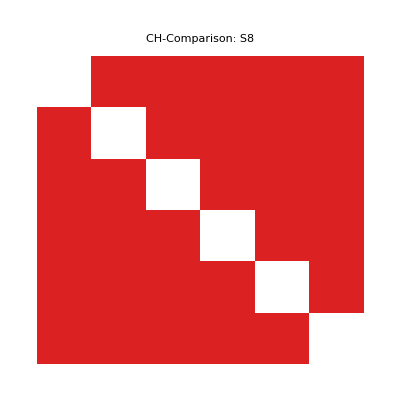
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | GrayLevel[1]

```mathematica
dataTimeStepsArray=
Map[Function[y,ArrayPlot[dataToPlot2[[y]],PlotLabel->"CH-Comparison: S"<>ToString[tsALLRed[[y]]], ColorFunction->"Rainbow",ImageSize->400,PlotLegends->Automatic,PlotRange->{dMin,dMax},
FrameTicks->{{Map[Function[x,{x,names[[x]]}],Range[6]],None},{Map[Function[x,{x,names[[x]]}],Range[6]],None}}]],Range[8]];
dataTimeStepsArrayOut=Grid[{dataTimeStepsArray[[1;;3]],dataTimeStepsArray[[4;;6]],AppendTo[dataTimeStepsArray[[7;;8]],White]},ItemSize->30]
```

```mathematica
SetDirectory["/home/carla/GDC/Comparisons/Persons/CH/"];
Export["gdc_COMP_CH_PERS_tables.jpeg",dataPersTableOut]
Export["gdc_COMP_CH_PERS_plot.jpeg",dataPersArrayOut]
Export["gdc_COMP_CH_TIME_plot.jpeg",dataTimeStepsArrayOut]
```

gdc_COMP_CH_PERS_tables.jpeg

gdc_COMP_CH_PERS_plot.jpeg

gdc_COMP_CH_TIME_plot.jpeg

```mathematica
(*ALTERNATIVE
cDLBMUR=Map[{Drop[tsAll,2][[#]],Map[compCHFunc[17,21,#, tatCH]&,Drop[tsAll,2]][[#]]}&,Range[Length[Drop[tsAll,2]]]]
cDLBLYE=Map[{Drop[tsAll,2][[#]],Map[compCHFunc[17,23,#, tatCH]&,Drop[tsAll,2]][[#]]}&,Range[Length[Drop[tsAll,2]]]]
cMURLYE=Map[{Drop[tsAll,2][[#]],Map[compCHFunc[21,23,#, tatCH]&,Drop[tsAll,2]][[#]]}&,Range[Length[Drop[tsAll,2]]]]

ListPlot[{cDLBMUR,cDLBLYE,cMURLYE},PlotLegends->{"DLBMUR", "DLBLYE", "MURLYE"},PlotStyle->{Red, Blue, Green},PlotLabel->"Comparison CH",PlotMarkers->{{"1",12}, {"2",12}, {"3",12}}, PlotRange->All]*)
```